#### 2.2.1 | Logistic Equation with Constant Injection

```mathematica
Quit[]
```

Variable Selection

```mathematica
q0=5;p0=3;k=7;β=4;u=3;
```

```mathematica
A = (β-u)
```

1

```mathematica
B = (1-(u/β))*k
```

7/4

```mathematica
q2[t_] := (B*q0)/(q0+(B-q0)*Exp[-A*t])
```

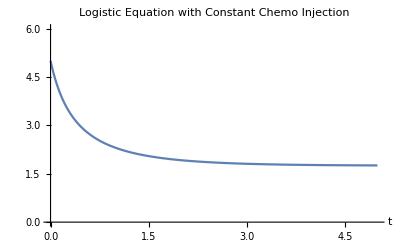

```mathematica
Plot[q2[t],{t,0,5},PlotRange->{0,6},PlotLabel->"Logistic Equation with Constant Chemo Injection",AxesLabel->Automatic]
```